## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[Plot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotPoints->200,PlotRange->All];
SetOptions[LogLinearPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotPoints->200,PlotRange->All];
SetOptions[ListLogLinearPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotRange->All];
SetOptions[ListLogLogPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotRange->All];
```

## Testing

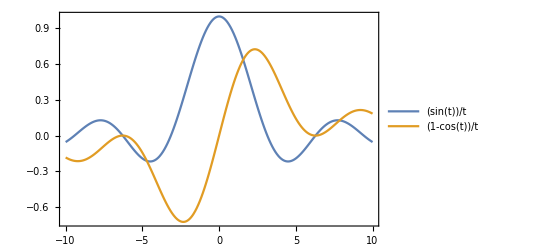

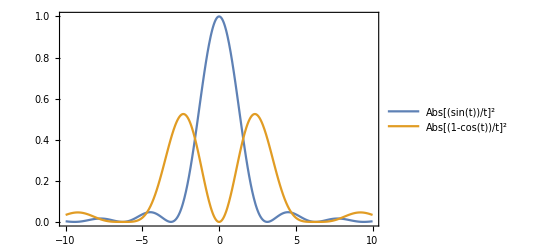

```mathematica
Plot[{Sin[t]/t,(1-Cos[t])/t},{t,-10,10},PlotLegends->"Expressions"]
Plot[{Abs[Sin[t]/t]^2,Abs[(1-Cos[t])/t]^2},{t,-10,10},PlotLegends->"Expressions"]
```

## Initialization

```mathematica
SetOptions[Plot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotPoints->200,PlotRange->All];
SetOptions[LogLinearPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotPoints->200,PlotRange->All];
SetOptions[ListLogLinearPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotRange->All];
SetOptions[ListLogLogPlot,Frame->True,ImageSize->Scaled[.7],FrameTicks->All,LabelStyle->Directive[FontSize->14,Black,FontOpacity->0.999,FontFamily->"Helvetica"],FrameTicksStyle->Directive[FontSize->12,Black,Plain],PlotRange->All];
```

### blah

```mathematica
e[t_,ω_,ϵ_]:=Sin[ω t]/t-Sin[ϵ t]/t
```

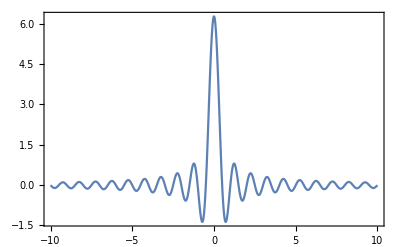

```mathematica
Plot[e[t,2π,.01],{t,-10,10}]
```

```mathematica
y=Integrate[e[t, ω], {t, -x, x}]
```

-2 SinIntegral[x ϵ]+2 SinIntegral[x ω]

```mathematica
y/.{x->10,ω->15000}
```

2 SinIntegral[150000]

```mathematica
N[SinIntegral[150000]]
N[π/2]
```

1.5708

1.5708

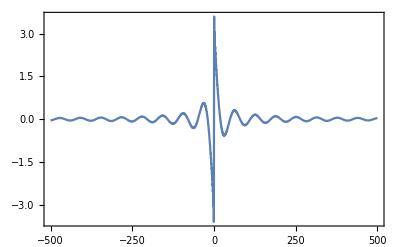

```mathematica
Plot[-2 SinIntegral[x 0.1]+2 SinIntegral[x 2π],{x,-500,500}]
```

```mathematica
z = Sin[ω t]/t-π
```

-π+Sin[t ω]/t

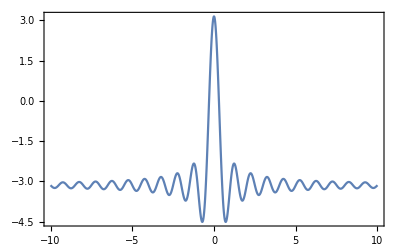

```mathematica
Plot[z/.{ω->2π,t->tr},{tr,-10,10}]
```

```mathematica
NIntegrate[z/.{ω->2π,t->tr},{tr,-10,10}]
```

-59.7221